# Fig. 4: Wigner Distributions

## 1. Packages and Fock-Space Cutoff

```mathematica
Needs[  "Wolfram`QuantumFramework`"];
```

```mathematica
Needs[  "Wolfram`QuantumFramework`SecondQuantization`"];
```

```mathematica
SetFockSpaceSize[ 80];
```

```mathematica
ClearAll[ ψi, displaced, Φ];
```

## 2. Photon-Added Cat State

```mathematica
ψi[ m_, r_, ϕ_, φ_] := ψi[ m, r, ϕ, φ] = Nest[ SuperDagger[ AnnihilationOperator[ ]][ #1] & , CatState[ ][ Association[ α -> N[ r*Exp[ I*ϕ]], ϕ -> N[ φ]]], m][ "Normalize"];
```

## 3. Displaced and Postselected States

```mathematica
displaced[ m_, r_, ϕ_, φ_, s_] := displaced[ m, r, ϕ, φ, s] = With[ {ψ = ψi[ m, r, ϕ, φ]}, (DisplacementOperator[ #1][ ψ] & ) /@ {N[ s]/2, -N[ s]/2}];
```

```mathematica
Φ[ m_, r_, ϕ_, φ_, s_, δ1_, δ2_] := With[ {Aw = Exp[ I*N[ δ1]]*Tan[ N[ δ2]/2], ab = displaced[ m, r, ϕ, φ, s]}, ((1 + Aw)*ab[ [ 1]] + (1 - Aw)*ab[ [ 2]])[ "Normalize"]];
```

## 4. Fixed Parameters

```mathematica
r = 1;
```

```mathematica
ϕ = Pi/2;
```

```mathematica
φ = Pi;
```

```mathematica
δ1 = Pi/2;
```

```mathematica
δ2 = 8*(Pi/9);
```

## 5. Wigner Distributions

### s = 0

```mathematica
W0 = Table[ WignerRepresentation[ Φ[ m, r, ϕ, φ, 0, δ1, δ2], {-5, 5}, {-5, 5}], {m, 0, 2}];
```

### s = 1

```mathematica
W1 = Table[ WignerRepresentation[ Φ[ m, r, ϕ, φ, 1, δ1, δ2], {-5, 5}, {-5, 5}], {m, 0, 2}];
```

### s = 2

```mathematica
W2 = Table[ WignerRepresentation[ Φ[ m, r, ϕ, φ, 2, δ1, δ2], {-5, 5}, {-5, 5}], {m, 0, 2}];
```

## 6. Color Scale

```mathematica
wrange = {-0.3, 0.3};
```

```mathematica
seismicColors = {RGBColor[ 0, 0, 0.3], RGBColor[ 0, 0, 1], White, RGBColor[ 1, 0, 0], RGBColor[ 0.5, 0, 0]};
```

```mathematica
seismicCF[ t_] := Blend[ seismicColors, Clip[ t, {0, 1}]];
```

## 7. Panel Labels and Axis Ticks

```mathematica
labels = {"(a)", "(b)", "(c)", "(d)", "(e)", "(f)", "(g)", "(h)", "(l)"};
```

```mathematica
sVals = {0, 0, 0, 1, 1, 1, 2, 2, 2};
```

```mathematica
axisSpec = Table[ {i > 6, Mod[ i, 3] == 1}, {i, 9}];
```

```mathematica
majorVals = Range[ -4, 4, 2];
```

```mathematica
minorVals = Complement[ Range[ -5, 5, 0.5], majorVals];
```

```mathematica
blankTicks = Join[ ({#1, "", {0.023, 0}} & ) /@ majorVals, ({#1, "", {0.01, 0}} & ) /@ minorVals];
```

## 8. Density-Plot Format

```mathematica
makePlot[ fun_, lab_, sVal_, {showX_, showY_}] := Module[ {padL = If[ showY, 100, 5], padB = If[ showX, 95, 5]}, DensityPlot[ fun[ x, p], {x, -5, 5}, {p, -5, 5}, PlotPoints -> 120, ColorFunction -> (seismicCF[ Rescale[ #1, wrange]] & ), ColorFunctionScaling -> False, PlotRange -> All, PlotRangePadding -> None, Frame -> True, FrameStyle -> Directive[ Black, AbsoluteThickness[ 2.2]], FrameTicks -> {{If[ showY, Automatic, blankTicks], blankTicks}, {If[ showX, Automatic, blankTicks], blankTicks}}, FrameLabel -> {{If[ showY, Style[ "p", 38, Black], None], None}, {If[ showX, Style[ "x", 38, Black], None], None}}, FrameTicksStyle -> Directive[ Black, 34], LabelStyle -> Directive[ Black, 1], Epilog -> {Text[ Style[ lab, 40,  Black, FontFamily -> "Times New Roman"], Scaled[ {0.13, 0.88}]], Text[ Style[ Row[ {Style[ "s", Italic], " = ", sVal}], 40,  Black, FontFamily -> "Times New Roman"], Scaled[ {0.5, 0.88}]]}, AspectRatio -> 1, ImagePadding -> {{padL, 5}, {padB, 5}}, ImageSize -> {305 + padL, 305 + padB}]];
```

## 9. Generate the Nine Panels

```mathematica
plots = MapThread[ makePlot, {Join[ W0, W1, W2], labels, sVals, axisSpec}];
```

## 10. Color Legend and Column Headers

```mathematica
legendCF = seismicCF[ Rescale[ #1, wrange]] & ;
```

```mathematica
legend = BarLegend[ {legendCF, wrange}, LabelStyle -> Directive[ Black,  34], LegendMarkerSize -> {30, 900}, TicksStyle -> Directive[ Black,  34]];
```

```mathematica
mHeaders = {Row[ {Spacer[ 53], Style[ Row[ {Style[ "m", Italic], " = 0"}], 36, Black, FontFamily -> "Times New Roman"]}], Style[ Row[ {Style[ "m", Italic], " = 1"}], 36,  Black, FontFamily -> "Times New Roman"], Style[ Row[ {Style[ "m", Italic], " = 2"}], 36,  Black, FontFamily -> "Times New Roman"]};
```

## 11. Assemble and Display Fig. 4

```mathematica
mainGrid = Grid[ {mHeaders, plots[ [ 1 ;; 3]], plots[ [ 4 ;; 6]], plots[ [ 7 ;; 9]]}, Spacings -> {0., 0.}, Alignment -> {Center, Center}];
```

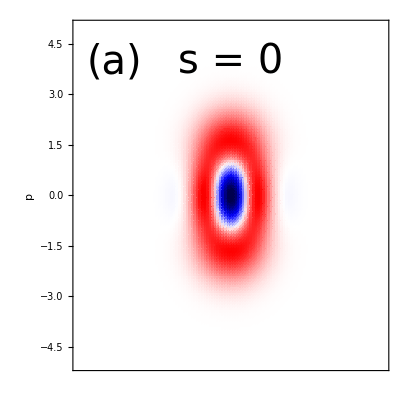
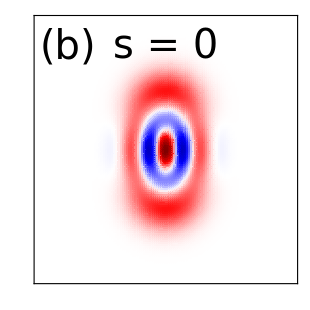
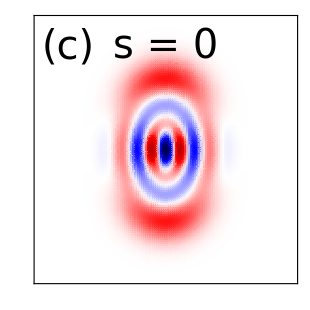
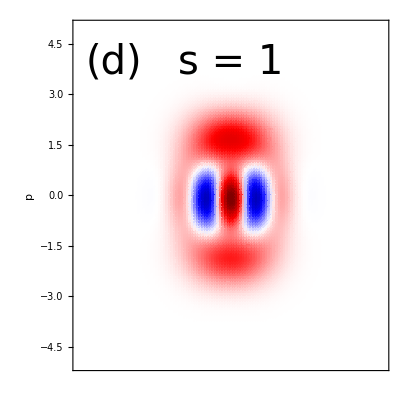
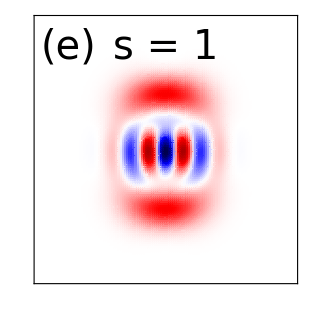
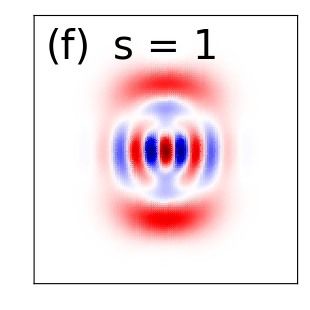
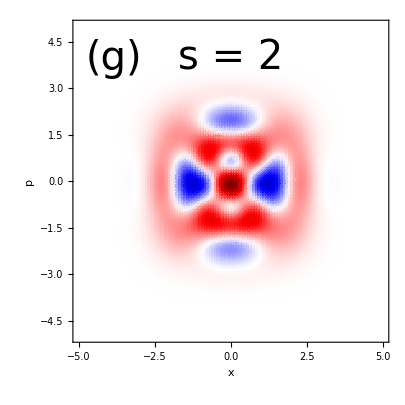
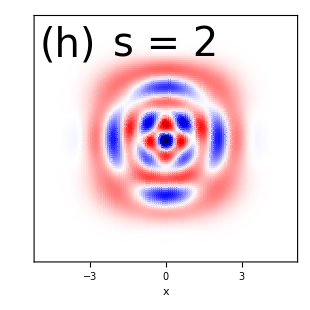
m = 0 | m = 1 | m = 2
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
b = Grid[ {{mainGrid, legend}}, Spacings -> {0.05, 0}, Alignment -> {Center, Center}]
```

## 12. Export PNG (Optional)

```mathematica
Export[ FileNameJoin[ {NotebookDirectory[ ], "Fig.4.png"}], ImageCrop[ Rasterize[ b, "Image", RasterSize -> 4200, Background -> White]], "PNG"];
```